# Al3X From Cylinder Detector Geometry

Run this first

### Defining cylinder geometry and functions for computing event yield

AL3X Comprises of cylindrical detector with a concentric cylindrical hole missing.
In the form x,y,z (of the first cap centre), length, inner and outer radius. All in m. x is up, y is to the right, and z is down the beampipe

```mathematica
cylinderDef={0,0, 5.25,12,0.85, 5};
```

#### Setting up cylinder definitions and relevant coordinate transformations

```mathematica
θfromη[η_]:=2 ArcCot[ⅇ^η];
ηfromθ[θ_]:=-Log[Tan[θ/2]];
```

Creates a parametric definition f(r,α) (caps) and f(l,α) (body). α runs from 0 to 2π while r and l are bounded by the input radius and length of the detector

```mathematica
planeSegmentsFromCylinder[cylinderDef_]:={
{cylinderDef[[1]]+r*Sin[α],cylinderDef[[2]]+r*Cos[α],cylinderDef[[3]]}
,
{cylinderDef[[1]]+r*Sin[α],cylinderDef[[2]]+r*Cos[α],cylinderDef[[3]]+cylinderDef[[4]]}
,
{cylinderDef[[1]] +cylinderDef[[5]]*Sin[α],cylinderDef[[2]]+cylinderDef[[5]]*Cos[α],cylinderDef[[3]]+l}
,
{cylinderDef[[1]] +cylinderDef[[6]]*Sin[α],cylinderDef[[2]]+cylinderDef[[6]]*Cos[α],cylinderDef[[3]]+l}
}
EndCapsCylinder[cylinderDef_]:={
{cylinderDef[[1]]+r*Sin[α],cylinderDef[[2]]+r*Cos[α],cylinderDef[[3]]}
,
{cylinderDef[[1]]+r*Sin[α],cylinderDef[[2]]+r*Cos[α],cylinderDef[[3]]+cylinderDef[[4]]}
}
BaseCylinder[cylinderDef_]:={
{cylinderDef[[1]] +cylinderDef[[5]]*Sin[α],cylinderDef[[2]]+cylinderDef[[5]]*Cos[α],cylinderDef[[3]]+l},
{cylinderDef[[1]] +cylinderDef[[6]]*Sin[α],cylinderDef[[2]]+cylinderDef[[6]]*Cos[α],cylinderDef[[3]]+l}
}
```

## Set up particle path geometry

{{s→17.3201,r→1.55671,α→1.5708},{s→9.45721,α→1.5708,l→4.16893}}

{{0.85,0.,9.41893},{1.55671,0.,17.25}}

{9.45721,17.3201}

3D modeling of surface and ray interactions:

-Graphics3D-

estimate geometric coverage

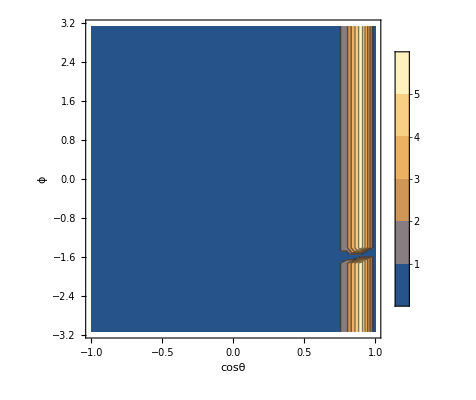

fraction of solid angle covered:

0.05

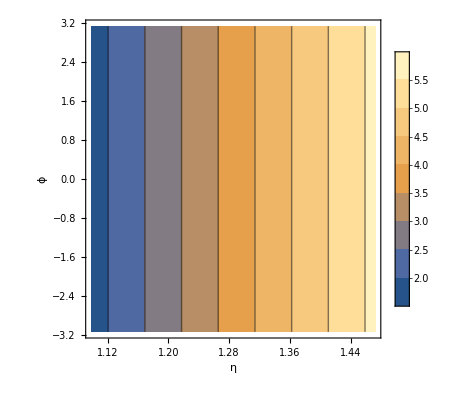

```mathematica
(*This sets the trajectory of the particle of interest that originates at the interaction point*)
(*{lineθ,lineϕ}={0.2,0};*)
{lineθ,lineϕ}={0.09,0};
currentline={0,0,0}+s{Sin[lineθ] Cos[lineϕ], Sin[lineθ] Sin[lineϕ],Cos[lineθ]};

(*Beam line axis from interaction point*)
Beamaxis={0,0,0}+s{0,0,1};

(*This determines the intersections of a particle trajectory (currentline) and a detector determined by cylinder dfinition *)
intersectionCylinderSolutions=Select[
Flatten[Solve[Evaluate[currentline==#],{s,r,α,l}]&/@(planeSegmentsFromCylinder[cylinderDef])/.C[1]-> 0,1]
,( (cylinderDef[[5]]≤ (r/.#)≤ cylinderDef[[6]]) && (s/.#)≥0 (*&& (α/.#)≥-3.1415*))||((0≤ (l/.#)≤ cylinderDef[[4]]) && (s/.#)≥0 )&]//Quiet

cylinderIntersectionPoints=If[Length[intersectionCylinderSolutions]>0,
Sort[currentline/.intersectionCylinderSolutions,#1.#1<#2.#2&]
,
{{ⅈ,ⅈ,ⅈ},{ⅈ,ⅈ,ⅈ}}
]

{√(cylinderIntersectionPoints[[1]].cylinderIntersectionPoints[[1]]),√(cylinderIntersectionPoints[[2]].cylinderIntersectionPoints[[2]])}

"3D modeling of surface and ray interactions:"
Show[
ParametricPlot3D[{
Evaluate[EndCapsCylinder[cylinderDef]]
},{r,cylinderDef[[5]],cylinderDef[[6]]},{α,0,2Pi},
PlotRange->{{-1,1},{-1,1},{0,2}}10,BoxRatios->{1,1,1},AxesLabel->{"x","y","z"},Mesh->False,PlotStyle->Evaluate[Directive[#,Opacity[0.4]]&/@{Red,Red,Blue,Blue,Green,Green}]]
,
ParametricPlot3D[{
Evaluate[BaseCylinder[cylinderDef]]
},{α,0,2Pi},{l,0,cylinderDef[[4]]},BoxRatios->{1,1,1},AxesLabel->{"x","y","z"},Mesh->False,
PlotStyle->Evaluate[Directive[#,Opacity[0.4]]&/@{Red,Red,Blue,Blue,Green,Green}]]
,
ParametricPlot3D[currentline,{s,0,10000},BoxRatios->{1,1,1},AxesLabel->{"x","y","z"}]
,
ParametricPlot3D[Beamaxis,{s,-1000,10000},BoxRatios->{1,1,1},AxesLabel->{"x","y","z"},PlotStyle->{Gray}]
,
ListPointPlot3D[cylinderIntersectionPoints,PlotStyle->{Red,PointSize[.02]}]
]

"estimate geometric coverage"
L2mL1Cylasfncosθϕ=Flatten[Table[{cosθ,ϕ,

{lineθ,lineϕ}={ArcCos[cosθ],ϕ};
currentline={0,0,0}+s{Sin[lineθ] Cos[lineϕ], Sin[lineθ] Sin[lineϕ],Cos[lineθ]};

intersectionCylinderSolutions=Select[
Flatten[Solve[Evaluate[currentline==#],{s,r,α,l}]&/@(planeSegmentsFromCylinder[cylinderDef])/.C[1]-> 0,1]
,( (cylinderDef[[5]]≤ (r/.#)≤ cylinderDef[[6]] ) && (s/.#)≥0 )||((0≤ (l/.#)≤ cylinderDef[[4]]) && (s/.#)≥0 )&]//Quiet;

cylinderIntersectionPoints=If[Length[intersectionCylinderSolutions]>0,
Sort[currentline/.intersectionCylinderSolutions,#1.#1<#2.#2&]
,
{{ⅈ,ⅈ,ⅈ},{ⅈ,ⅈ,ⅈ}}
];

√(cylinderIntersectionPoints[[2]].cylinderIntersectionPoints[[2]])-√(cylinderIntersectionPoints[[1]].cylinderIntersectionPoints[[1]])
}
,{cosθ,1,-1,-0.1},{ϕ,-π,π,π/20}],1];

ListContourPlot[L2mL1Cylasfncosθϕ,PlotLegends->Automatic, FrameLabel->{"cosθ","ϕ"}]


"fraction of solid angle covered:"
1/(4π)(Transpose[Select[L2mL1Cylasfncosθϕ,#[[3]]>0&]][[1]]//Max[#]-Min[#]&)(Transpose[Select[L2mL1Cylasfncosθϕ,#[[3]]>0&]][[2]]//Max[#]-Min[#]&)


ListContourPlot[{ArcCos[#[[1]]]//ηfromθ,#[[2]],#[[3]]}&/@Select[L2mL1Cylasfncosθϕ,#[[3]]>0&],PlotLegends->Automatic, FrameLabel->{"η","ϕ"}]
```

## Define particle entry and exit points and setting up event yield

```mathematica
DecayProb[L1_?NumericQ,L2_?NumericQ,bλ_?NumericQ]:=ⅇ^(-L1/bλ)-ⅇ^(-L2/bλ);
```

CylinderDetectorL1L2m takes in the cylinder definition and defining variables of a a particle trajectory, θ and ϕ. From these, it determines the intercept points L1 and L2 and outputs their radial distance from the interaction point. Trajectories with no intersection return complex values.

```mathematica
CylinderDetectorL1L2m[θ_,ϕ_,cylinderDef_]:=Module[{cosθ},
cosθ=Cos[θ];
{lineθ,lineϕ}={ArcCos[cosθ],ϕ};
currentline={0,0,0}+s{Sin[lineθ] Cos[lineϕ], Sin[lineθ] Sin[lineϕ],Cos[lineθ]};

intersectionCylinderSolutions=Select[
Flatten[Solve[Evaluate[currentline==#],{s,r,α,l}]&/@(planeSegmentsFromCylinder[cylinderDef])/.C[1]-> 0,1]
,( (cylinderDef[[5]]≤ (r/.#)≤ cylinderDef[[6]] ) && (s/.#)≥0 )||((0≤ (l/.#)≤ cylinderDef[[4]]) && (s/.#)≥0 )&]//Quiet;

cylinderIntersectionPoints=If[Length[intersectionCylinderSolutions]>0,
Sort[currentline/.intersectionCylinderSolutions,#1.#1<#2.#2&]
,
{1/(√3){ⅈ,ⅈ,ⅈ},1/(√3){ⅈ,ⅈ,ⅈ}}
];

{√(cylinderIntersectionPoints[[1]].cylinderIntersectionPoints[[1]]),√(cylinderIntersectionPoints[[2]].cylinderIntersectionPoints[[2]])}
];
```

As the name implies, this function determines the values of Cos θ and ϕ that lead to trajectories that reach the detector. The interior table creates a list of values for each angular coordinate pair that has the form {Cos θ, ϕ, distance travelled in the detector}. If the angular coordinates do not lead to an intersecting trajectory, the value of the third entry is set to 0. The final several lines convert this information into a range of angular values {Cos θ min, Cos θ max}, {ϕ min, ϕ max} while making certain that we don’t extend beyond the coordinate limits due to the addition of the variable steps.

```mathematica
Findcosθϕrange[cylinderDef_,cosθstep_:2/20,ϕstep_:2π/20]:=Module[{},
L2mL1Cylasfncosθϕ=Flatten[Table[{cosθ,ϕ,

{lineθ,lineϕ}={ArcCos[cosθ],ϕ};
currentline={0,0,0}+s{Sin[lineθ] Cos[lineϕ], Sin[lineθ] Sin[lineϕ],Cos[lineθ]};

intersectionCylinderSolutions=Select[
Flatten[Solve[Evaluate[currentline==#],{s,r,α,l}]&/@(planeSegmentsFromCylinder[cylinderDef])/.C[1]-> 0,1]
,((0≤ (r/.#)≤ cylinderDef[[5]]) && (s/.#)≥0 )||((0≤ (l/.#)≤ cylinderDef[[4]]) && (s/.#)≥0 )&]//Quiet;

cylinderIntersectionPoints=If[Length[intersectionCylinderSolutions]>0,
Sort[currentline/.intersectionCylinderSolutions,#1.#1<#2.#2&]
,
{{ⅈ,ⅈ,ⅈ},{ⅈ,ⅈ,ⅈ}}
];

√(cylinderIntersectionPoints[[2]].cylinderIntersectionPoints[[2]])-√(cylinderIntersectionPoints[[1]].cylinderIntersectionPoints[[1]])
}
,{cosθ,1,-1,-cosθstep},{ϕ,-π,π,ϕstep}],1];


preRange ={(Transpose[Select[L2mL1Cylasfncosθϕ,#[[3]]>0&]][[1]]//{Min[#]-cosθstep,Max[#]+cosθstep}&)
,(Transpose[Select[L2mL1Cylasfncosθϕ,#[[3]]>0&]][[2]]//{Min[#]-ϕstep,Max[#]+ϕstep}&)
};

range ={{If[preRange[[1]][[1]]<-1,-1,preRange[[1]][[1]]],If[preRange[[1]][[2]]>1,1,preRange[[1]][[2]]]},{If[preRange[[2]][[1]]<-Pi,-Pi,preRange[[2]][[1]]],If[preRange[[2]][[2]]>Pi,Pi,preRange[[2]][[2]]]}}

];
```

```mathematica
(*Findcosθϕrange[cylinderDef] Test to ensure this is working as planned*)
```

```mathematica
ComputeDecayEfficiencyCylinderDetector[θblist_, currentcτmeters_, cylinderDef_,currentcosθϕrange_]:=Module[{θblistflat},
θblistflat=Flatten[θblist,1];
(*we choose ϕ randomly to lie within the range covered by the box detector, and weigh accordingly*)
(*(this would obviously not be ok if we wanted to detect two particles per event, since the ϕ correlations have been thrown out, but doesn't matter for us)*)
(currentcosθϕrange[[2]][[2]]-currentcosθϕrange[[2]][[1]])/(2π)( Sum[
X1=θblistflat[[i]];
PX1inCyl=(DecayProb[#1⟦1⟧,#1⟦2⟧,currentcτmeters X1⟦2⟧]&)[CylinderDetectorL1L2m[X1⟦1⟧,RandomReal[currentcosθϕrange[[2]]],cylinderDef]];
{PX1inCyl,PX1inCyl^2}
,{i,1,Length[θblistflat]}]
//{#[[1]],√(#[[2]])}&
)/Length[θblist]//Re
]
```

From the below  functions, it appears that the .dat files are organized in scattering events that have a certain number dark pions (points). The three terms of the points within each entry are θ, ϕ, and the boost factor (I think).

### Read In Data:

```mathematica
SetDirectory[NotebookDirectory[]<>"/PythiaSims/1kEvents"]
(* 
Beam energy = 13 TeV
Cross sections from 
https://twiki.cern.ch/twiki/bin/view/LHCPhysics/SUSYCrossSections13TeVstopsbottom
use number of dark colours = 3, cross section scales linearly with Ncd 
*)
(*LLPxsecfb[1750]=3*43.; (*cross section associated with data set*)
LLPxsecfb[1400]=3*1840.; (*cross section associated with data set*)
LLPxsecfb[10400]=3*1840.; (*cross section associated with data set*)
LLPxsecfb[10750]=3*43.; (*cross section associated with data set*)*)
LLPxsecfb[11000]=3*6.2; (*cross section associated with data set*)
LLPxsecfb[11500]=3*0.25; (*cross section associated with data set*)


θϕbList[1100]=ReadList["EJ1_1000.dat"][[1]];  (*data*)
θϕbList[4100]=ReadList["EJ4_1000.dat"][[1]];  (*data*)
θϕbList[8100]=ReadList["EJ8_1000.dat"][[1]];  (*data*)
θϕbList[1150]=ReadList["EJ1_1500.dat"][[1]];  (*data*)
θϕbList[4150]=ReadList["EJ4_1500.dat"][[1]];  (*data*)
θϕbList[8150]=ReadList["EJ8_1500.dat"][[1]];  (*data*)
fileIDlist={1100,4100,8100,1150,4150,8150}; (*list of labels of all data set. Will be looped over later.*)

Lumiifb=3000;
```

/Users/dylanlinthorne/Dropbox/New Detectors/PythiaSims/1kEvents

```mathematica
(*This routine computes the point of entry and exit for each particle, along the line of motion.*)
L1L2[event_]:=
Table[
CylinderDetectorL1L2m[point[[1]],point[[2]],cylinderDef]~Join~{point[[3]]}
,{point,event}];
```

```mathematica
(*This routine computes the probability of at least one and at least 2 vertices in the detector. The inputs is are the list of (entrypoint,exitpoints) for each event, obtained with the previous routine, as well as the lifetime.*)
EventProb[event_,logcτ_]:=(Module[{problist},
problist=Re[DecayProb[#[[1]],#[[2]],#[[3]]*10^logcτ]]&/@event;
{1-(Times@@(1-problist)),
1-(Times@@(1-problist))-Sum[Times@@(ReplacePart[#,i->1-#[[i]]]&@(1-problist)),{i,Length[problist]}]}
])
```

```mathematica
CylinderDetectorL1L2m[.2,.5,cylinderDef];
```

### Parallel Calculation of Efficiency and Variance:

```mathematica
SetDirectory[NotebookDirectory[]<>"/EJData"]
```

/Users/dylanlinthorne/Dropbox/New Detectors/EJData

```mathematica
log10cτlist={-1,-.75,-.5,-.25,0,0.25,0.5,0.75,1,1.25,1.5,1.75,2,2.25,2.5,3,3.5,4,4.5,7};
Do[
nevents=Length[θϕbList[ID]];
L1L2list=ParallelMap[L1L2,θϕbList[ID]];

efflist[ID]=ParallelTable[{logτ}~Join~Mean[EventProb[#,logτ]&/@L1L2list],{logτ,log10cτlist}];

variancelist[ID]=ParallelTable[{logτ}~Join~Variance[EventProb[#,logτ]&/@L1L2list],{logτ,log10cτlist}];

Export["alex_efflist_"<>ToString[ID]<>".txt",efflist[ID],"Table"];
Export["alex_varlist_"<>ToString[ID]<>".txt",variancelist[ID],"Table"];

,{ID,fileIDlist}]
```

Join::heads: Heads List and Mean at positions 1 and 2 are expected to be the same.

General::stop: Further output of Join::heads will be suppressed during this calculation.

Join::heads: Heads List and Mean at positions 1 and 2 are expected to be the same.

General::stop: Further output of Join::heads will be suppressed during this calculation.

Join::heads: Heads List and Mean at positions 1 and 2 are expected to be the same.

General::stop: Further output of Join::heads will be suppressed during this calculation.

## Format empty cells:

```mathematica
NotebookDelete/@Select[Cells[GeneratedCell->False],StringMatchQ[First@FrontEndExecute[FrontEnd`ExportPacket[NotebookRead@#,"InputText"]],(" "|"\t"|"\r"|"\n"|"
")...]&]
```

{Null}